```mathematica
SetDirectory["/home/hall/w2013/stat245/scripts_8"]
```

/home/hall/w2013/stat245/scripts_8

```mathematica
d=Import["2","Table"]
```

{{0.34,1.38,-0.65,0.68,1.4,-0.88,-0.3,-1.18,0.5,-1.75},{0.27,1.34,-0.53,0.35,1.28,-0.98,-0.72,-0.81,0.64,-1.59}}

```mathematica
data=Transpose[d]
```

{{0.34,0.27},{1.38,1.34},{-0.65,-0.53},{0.68,0.35},{1.4,1.28},{-0.88,-0.98},{-0.3,-0.72},{-1.18,-0.81},{0.5,0.64},{-1.75,-1.59}}

```mathematica
m=Map[Function[{1,First[#1]}],data]
```

{{1,0.34},{1,1.38},{1,-0.65},{1,0.68},{1,1.4},{1,-0.88},{1,-0.3},{1,-1.18},{1,0.5},{1,-1.75}}

```mathematica
b=Map[Rest,data]
```

{{0.27},{1.34},{-0.53},{0.35},{1.28},{-0.98},{-0.72},{-0.81},{0.64},{-1.59}}

```mathematica
LeastSquares[m,b]
```

{{-0.033397},{0.904414}}

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.033397+0.904414 x]

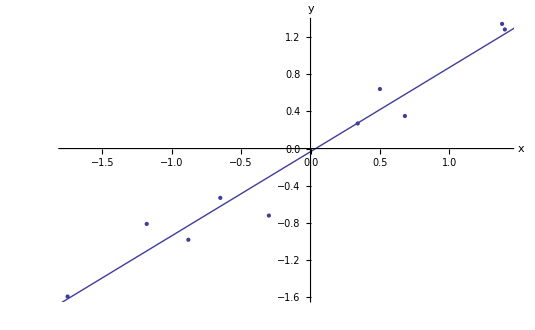

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,-2,2}],AxesLabel->{x,y}]
```

```mathematica
data2=Map[Reverse,data]
```

{{0.27,0.34},{1.34,1.38},{-0.53,-0.65},{0.35,0.68},{1.28,1.4},{-0.98,-0.88},{-0.72,-0.3},{-0.81,-1.18},{0.64,0.5},{-1.59,-1.75}}

```mathematica
lm2=LinearModelFit[data2,y,y]
```

FittedModel[0.0331257+1.05501 y]

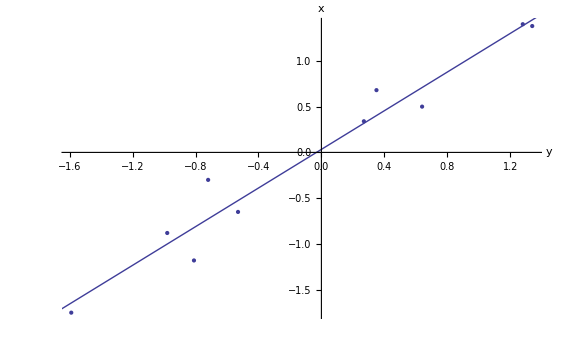

```mathematica
Show[ListPlot[data2],Plot[lm2[y],{y,-2,2}],AxesLabel->{y,x}]
```

```mathematica
1/1.05501
```

0.947858